-Graphics3D-

-Graphics3D-

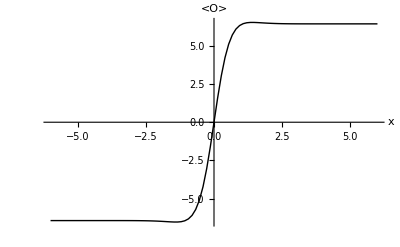

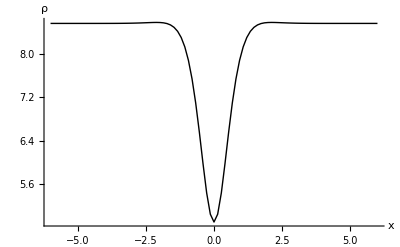

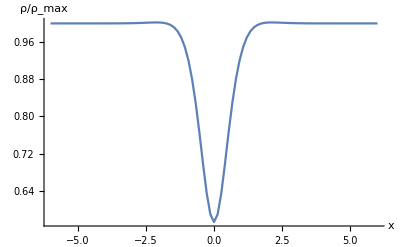

0.572606

```mathematica
Clear["Global`*"]
μ=5.5;m=25;n=141;L=6.0;
f[w_]=1-w^3;
fp[w_]=f'[w];
y1=Table[Cos[(i π)/(m-1.0)],{i,0,m-1}];
y2=Table[Cos[(i π)/(n-1.0)],{i,0,n-1}];
c1=Table[1.0,{i,m}];c1⟦1⟧=2.0;c1⟦m⟧=2.0;
c2=Table[1.0,{i,n}];c2⟦1⟧=2.0;c2⟦n⟧=2.0;
dz=2Table[If[i≠j,c1⟦i⟧/c1⟦j⟧(-1)^(i+j)/(y1⟦i⟧-y1⟦j⟧),0],{i,m},{j,m}];
dz-=DiagonalMatrix[Total[dz,{2}]];
dx=1/L Table[If[i≠j,c2⟦i⟧/c2⟦j⟧(-1)^(i+j)/(y2⟦i⟧-y2⟦j⟧),0],{i,n},{j,n}];
dx-=DiagonalMatrix[Total[dx,{2}]];
dx=Transpose[dx];
d2z=dz.dz;d2x=dx.dx;
z=(1+y1)/2;
x=L y2;
fz=f[z];fpz=fp[z];
ψ=Table[Subscript[a, i,j],{i,m},{j,n}];
At=Table[Subscript[b, i,j],{i,m},{j,n}];
Rψ=(z-At^2)ψ-ψ.d2x+3*z^2(dz.ψ)-fz*(d2z.ψ);
RAt=-fz*(d2z.At)+3*z^2(dz.At)-At.d2x+(2 ψ^2)At;
Rψ⟦-1⟧=ψ⟦-1⟧;
Rψ⟦All,{1,-1}⟧=ψ.dx⟦All,{1,-1}⟧;
RAt⟦-1⟧=At⟦-1⟧-μ;
RAt⟦All,{1,-1}⟧=At.dx⟦All,{1,-1}⟧;
eqs=Table[Rψ⟦i,j⟧==0,{i,m},{j,n}]~Join~Table[RAt⟦i,j⟧==0,{i,m},{j,n}];
init=Table[{Subscript[a, i,j],4 z⟦i⟧Tanh[x⟦j⟧]},{i,m},{j,n}]~Join~Table[{Subscript[b, i,j],μ(1-z⟦i⟧)},{i,m},{j,n}];
fr=FindRoot[Flatten[eqs,1],Flatten[init,1]];
ψ=ψ/.fr;
At=At/.fr;
ListPlot3D[Flatten[Table[{z⟦i⟧,x⟦j⟧,ψ⟦i,j⟧},{i,m},{j,n}],1],AxesStyle->{Directive[Black,16],Directive[Black,16],Directive[Black,16]}]
ListPlot3D[Flatten[Table[{z⟦i⟧,x⟦j⟧,At⟦i,j⟧},{i,m},{j,n}],1],PlotRange->All,AxesStyle->{Directive[Black,16],Directive[Black,16],Directive[Black,16]}]
ListPlot[Transpose[{x,dz⟦-1⟧.ψ}],Joined->True,PlotRange->All,AxesLabel->{HoldForm[x],RawBoxes[RowBox[{"<","O",">"}]]},PlotLabel->None,LabelStyle->{GrayLevel[0]},PlotStyle->{Thick,Black},AxesStyle->{Directive[Black,16],Directive[Black,16]}]
ListPlot[Transpose[{x,-dz⟦-1⟧.At}],Joined->True,PlotRange->All,AxesLabel->{HoldForm[x],RawBoxes[RowBox[{"ρ"}]]},PlotLabel->None,LabelStyle->{GrayLevel[0]},PlotStyle->{Thick,Black},AxesStyle->{Directive[Black,16],Directive[Black,16]}]
ListPlot[Transpose[{x,dz⟦-1⟧.At/dz⟦-1⟧.At⟦All,1⟧}],Joined->True,PlotRange->All,AxesLabel->{HoldForm[x],RawBoxes[RowBox[{"ρ/ρ_max"}]]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
dz⟦-1⟧.At⟦All,(n+1)/2⟧/dz⟦-1⟧.At⟦All,1⟧
```